# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

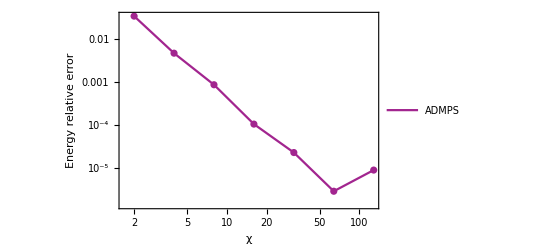

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

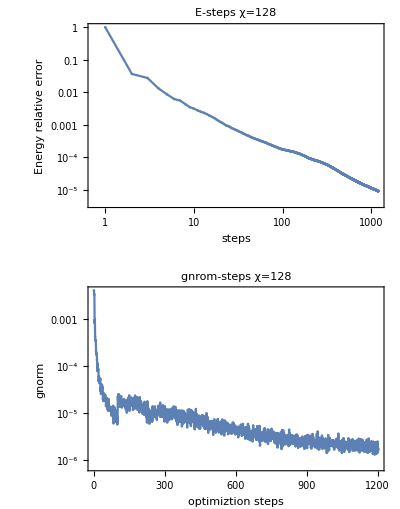

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=0.5

#### relative error-χ

error exponentially-dependent on χ

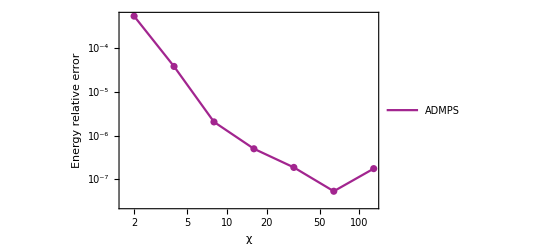

{{2,0.000547469},{4,0.0000384942},{8,2.06229×10^-6},{16,4.99614×10^-7},{32,1.86865×10^-7},{64,5.3171×10^-8},{128,1.75275×10^-7}}

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}]/4;
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
AD MPS energy aberror
```

#### relative error-steps

error exponentially-dependent on steps

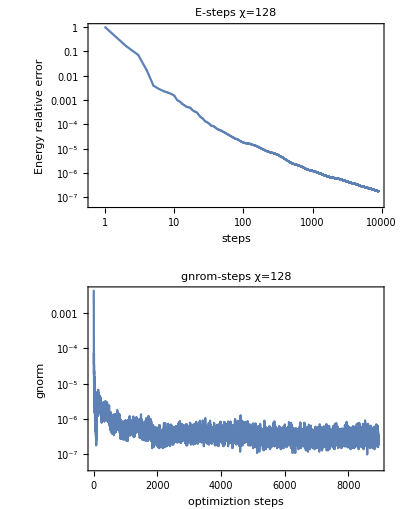

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```